```mathematica
(*Compute the repo root from the notebook location*)repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
ClearAll[RichardsonResum];
RichardsonResum[PartSum_,n_]:=With[{d=Length[PartSum]-n-1},Sum[PartSum[[Length[PartSum]+k-n]](d+k)^n(-1)^(k+n)/k!/(n-k)!,{k,0,n}]];
```

```mathematica
TTD[{varpi2_, varpi3_}] := {varpi2/(2Pi I),-4(varpi3)/(2Pi I)^2+1/6};
```

```mathematica
F1PeriodsN[λ_,ut_,Nn_,Nr_]:=Module[{varpi2tab,varpi3tab,varpi2resum,varpi3resum,varpi2,varpi3,k,l},
varpi2tab=Table[(-1/ut)^n Sum[k=n-2l; 
(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) /(k+2l),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi3tab=Table[(-1/ut)^n Sum[k=n-2l; 
λ^(l-k)(If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 (k+2 l) l! Gamma[1+k]^2),
0 (2 Log[ut]-1/4 Log[λ])(k+2l)!/((l)!(k!)^2(l-k)!)/(k+2l)
+(( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k+2 l) (k!)^2 l! Gamma[1-k+l]))]+ (2  (k+2 l)!)/((k+2 l)^2 (k!)^2 l! (-k+l)!)),
{l,0,Floor[n/2]}],{n,1,Nn}];
varpi2resum=RichardsonResum[Accumulate[varpi2tab],Nr];
varpi3resum=RichardsonResum[Accumulate[varpi3tab],Nr];
(* replace ut by -ut in argument of Log !! *)
varpi2=-Log[-ut]+varpi2resum;
varpi3=Log[-ut] ^2+(-Log[-ut]+varpi2resum)(2Log[-ut]-1/4 Log[λ])+Log[λ]^2/8+varpi3resum;
{varpi2, varpi3} ];
```

```mathematica
uAll = SortBy[u/.NSolve[MirrorCurveDelta[N[14/100,100],u]==0,u], Abs]
u0 = First[%]
```

{-0.140384165722560025085334850944404544758757646148360754470903121186852142611492324101671917874538573,0.319072002781633162398024743817721983737572351406865920072961972792610075760440332824483631616343892,-0.182829265962636673359934071508775987509227433400592764999519889703883028883793573485955643308820079-0.287265930207389072276879982850280049752069309971663778316157680103138794146719527521589378634373586 ⅈ,-0.182829265962636673359934071508775987509227433400592764999519889703883028883793573485955643308820079+0.287265930207389072276879982850280049752069309971663778316157680103138794146719527521589378634373586 ⅈ}

-0.140384165722560025085334850944404544758757646148360754470903121186852142611492324101671917874538573

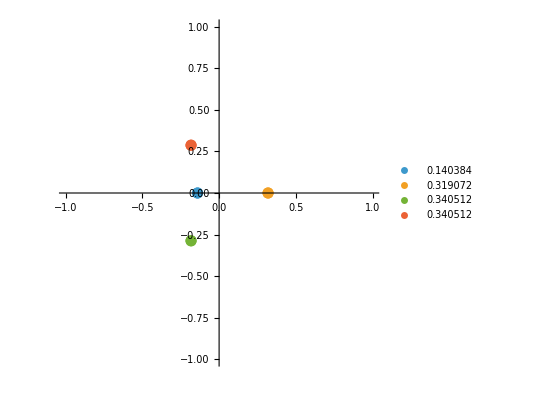

```mathematica
ComplexListPlot[Thread[{uAll}],
PlotRange->{{-1,1},{-1,1}},
PlotStyle->{PointSize[.02]},
PlotLegends->N[Abs/@uAll],
AspectRatio->1
]
```

```mathematica
With[{m=N[1,100]}, Module[{per},
uAll = SortBy[u/.NSolve[MirrorCurveDelta[m,u]==0,u], Abs];
u0 = First[uAll];
per = F1PeriodsN[m, -1/u0, 500, 10];
TTD[per]
]]
```

{0.184193533083328278281112707418642099123491138780336378507277294210087755177 ⅈ,4.4058793789548923114299493893660435827970370969×10^-29}

```mathematica
{Tp,TDp,mp}/.First@Solve[Thread[MonodromySqrtLV[{Tp,TDp,mp}]=={T,TD,m}],{Tp,TDp,mp}]//Expand
%/.{T->.184I, TD->0,m->1}
```

{-1/2+T,1-m/2-4 T+TD,m}

{-0.5+0.184 ⅈ,0.5-0.736 ⅈ,1}

```mathematica
With[{m=N[lam0,100]}, Module[{per},
uAll = SortBy[u/.NSolve[MirrorCurveDelta[m,u]==0,u], Abs];
u0 = First[uAll];
per = F1PeriodsN[m, -1/u0, 500, 10];
TTD[per]
]]
```

{0.1667335798581584995333221423134376894983343245031362780684005111483093119553 ⅈ,1.9798022855210900816734134986397667629330985874407406966022505×10^-14}

```mathematica
Simplify[Abs[uvals[lam][[1]]]-Abs[uvals[lam][[2]]], 0<lam<1];
lam0 = lam/.FindRoot[%, {lam,N[32/100]}, WorkingPrecision->100]
```

0.3347475541335620739910429101049186782909686615723576658234288145109227358626859229430235769474821778

```mathematica
Simplify[Abs[uvals[lam][[1]]]-Abs[uvals[lam][[4]]], 0<lam<1];
lam1 = lam/.FindRoot[%, {lam,N[30/100]}, WorkingPrecision->100]
```

0.2976376972440374015159448073635577988234049989812224393390535803422280948045410949887895399866664294

```mathematica
Precision[lam0]
```

100.

```mathematica
lam0
```

0.3347475541335620739910429101049186782909686615723576658234288145109227358626859229430235769474821778

```mathematica
With[{m=lam0+N[4/100,100]}, Module[{per},
uAll = SortBy[u/.NSolve[MirrorCurveDelta[m,u]==0,u], Abs];
u0 = Echo@First[uAll];
per = F1PeriodsN[m, -1/u0, 500, 10];
TTD[per]
]]
```

0.29959217059535264710261407303117155225677320201710601040741892899223724819530807521402448003828286

{0.1680004111247554848708674076609927380554651132879483844522914577087120460737 ⅈ,-1.9749650152220263695266757181485671620941888871654621786482×10^-17}

```mathematica
lam1
```

0.2976376972440374015159448073635577988234049989812224393390535803422280948045410949887895399866664294

```mathematica
With[{m=lam0-N[4/1000,100]}, Module[{per},
uAll = SortBy[u/.NSolve[MirrorCurveDelta[m,u]==0,u], Abs];
u0 = Echo@First[uAll];
per = F1PeriodsN[m, -1/u0, 500, 10];
TTD[per]
]]
```

0.302908172828837843180893763967263806781776452209108169022557825006643738254792236118090026138998747

{0.1666048036587454963954201964560757024981873372516759145569838682591407965077 ⅈ,2.8994207471265567766265638747588515534496628299012369362207944329×10^-11}

```mathematica
Series[ First@F1PeriodsN[m,-1/u,300,0]/.{Log[1/u]->-Log[u]},{u,0,300}];
expr = Abs[SeriesCoefficient[%,300]]^(1/300)/.{m->m1+I m2};
```

```mathematica
1/expr/.{m1->.33,m2->0.}//N
```

0.31605+0. ⅈ

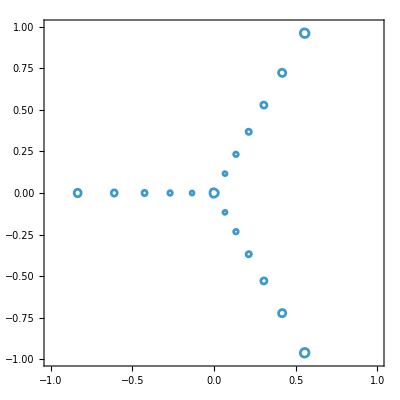

```mathematica
ContourPlot[Abs[expr]==1, {m1,-1,1},{m2,-1,1},
PlotPoints->200,
MaxRecursion->4
]
```

```mathematica
(* ChatGPT *)
M[bet_] := 3bet(1+bet)^(1/3)(1-2bet)^(-4/3);
R[bet_] := 1/3(1+bet)^(1/3)(1-2bet)^(2/3);
```

```mathematica
R[bet]/.First@Solve[M[bet]==Abs[N[29/100,100]],bet]
```

0.3061041061753398387541025054669658693602924869266658777969423114434266886917175391939044346436

```mathematica
Abs/@SortBy[uvals[N[29/100,100]],Abs]
```

{0.297080501557702840841904897202298699108201812498452597756216326071705746206574396332084334336426311,0.306104106175339838754102505466965869360292486926665877796942311443426688691717539193904434643563468,0.346183797515322437668461264028005268501607004992657606218398629015897074106281876468376137702284797,0.346183797515322437668461264028005268501607004992657606218398629015897074106281876468376137702284797}

```mathematica
MirrorCurveDelta[m,u]
```

m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4

```mathematica
D[MirrorCurveDelta[m,u], m]
```

1-16 m u^2-36 u^3+48 m^2 u^4

```mathematica
Solve[{m+u-8 m^2 u^2-36 m u^3-27 u^4+16 m^3 u^4==0,1-16 m^2 u-108 m u^2-108 u^3+64 m^3 u^3==0}, {m,u}]
```

{{m→(3 (-1)^(1/3))/(4 2^(2/3)),u→-1/3 (-2)^(1/3)},{m→-3/(4 2^(2/3)),u→2^(1/3)/3},{m→-3/4 (-1/2)^(2/3),u→1/3 (-1)^(2/3) 2^(1/3)}}

```mathematica
data = Table[{m1,m2,Min[Abs/@uvals[m1+I m2]]-(R[bet]/.First@NSolve[M[bet]==Abs[m1+I m2],bet])}, {m1,-2,2, .01},{m2,-2,2, .01}];
```

General::munfl: (-1.89+1.89 ⅈ)^6 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
Manipulate[ComplexListPlot[Thread[{SortBy[u/.NSolve[MirrorCurveDelta[m1+I m2,u]==0,u], Abs]}],
PlotRange->{{-1,1},{-1,1}},
PlotStyle->{PointSize[.02]},
AspectRatio->1
], {{m1,lam0},-1.,4.,.01},{{m2,0.},-1.,1.,.01}]
```

```mathematica
With[{m=lam0-N[4/100,100]}, Module[{per},
uAll = SortBy[u/.NSolve[MirrorCurveDelta[m,u]==0,u], Abs];
u0 = First[uAll];
Print[Abs[uAll]];
per = F1PeriodsN[m, -1/u0, 500, 10];
TTD[per]
]]
```

{0.302304024966957943799234251791547279068765042194786919431094773256929719753838891117585164756403616,0.305725252318861494900313087956950332205185710719388093235515860494002558639948770589375223782845935,0.34631866713547289293005723846124777762617542293125718324330262359170206038921436171818760773954086,0.34631866713547289293005723846124777762617542293125718324330262359170206038921436171818760773954086}

{-0.5-8.35228433718517995380701031736980385513541363503006548266625448989065675676547447523274106×10^13 ⅈ,1.625721708375408293617726034887331033370643098127193724151071147890701104871497×10^12+3.34091373487407100937573382796541907670634506507764061639420057603754588066939321944468496×10^14 ⅈ}

```mathematica
(* now with Richardson sum *)
F1dPeriodsN[λ_,ut_,Nn_,Nr_]:=Module[{om1tab,om2tab,om1resum, om2resum,k,l},
om1tab=Table[(-1/ut)^n Sum[k=n-2l;-(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) ,{l,0,Floor[n/2]}],{n,0,Nn}];
om2tab=Table[(-1/ut)^n Sum[k=n-2l; λ^(-k+l)(- If[k>l,((-1)^(k+l) Gamma[k-l] Gamma[1+k+2 l])/(4 l! Gamma[1+k]^2),0]+- If[k<=l&&k+2l>0,( (k+2 l)! (4 HarmonicNumber[k]+3 HarmonicNumber[l]+HarmonicNumber[-k+l]-8 HarmonicNumber[k+2 l]))/(4 (k!)^2 l! Gamma[1-k+l]),0]),{l,0,Floor[n/2]}],{n,0,Nn}];
om1resum=RichardsonResum[Accumulate[om1tab],Nr];
om2resum=RichardsonResum[Accumulate[om2tab],Nr];
om1resum
];
```

```mathematica
ser1 = Series[F1dPeriodsN[m,-1/u, 1000,0], {u,0,1000}];
```

```mathematica
ser1
```

-1-2 m u^2-6 u^3-6 m^2 u^4-60 m u^5+(-90-20 m^3) u^6-420 m^2 u^7-70 (m (24+m^3)) u^8+(-1680-2520 m^3) u^9-252 (m^2 (75+m^3)) u^10+O[u]^11

```mathematica
1/Abs[a1000]^(1/10000)/.{λ->N[29/100,100]}
```

0.306425296831552255318708373625586971105262718677392171884671457509699396261017577161826714601007023

```mathematica
a1000 = Sum[k=n-2l;-(k+2l)!/((l)!(k!)^2(l-k)!)λ^(l-k) ,{l,0,Floor[n/2]}]/.{n->10000};
```

```mathematica
(* ChatGPT *)
M[bet_] := 3bet(1+bet)^(1/3)(1-2bet)^(-4/3);
R[bet_] := 1/3(1+bet)^(1/3)(1-2bet)^(2/3);
```

```mathematica
R[bet]/.First@Solve[M[bet]==Abs[N[29/100,100]],bet]
```

0.3061041061753398387541025054669658693602924869266658777969423114434266886917175391939044346436

```mathematica
With[{m=N[121/100,100]}, Module[{per},
uAll = SortBy[u/.NSolve[MirrorCurveDelta[m,u]==0,u], Abs];
u0 = First[uAll];
per = F1PeriodsN[m, -1/u0, 500, 10];
TTD[per]
]]
```

{0.18857848045465604600923136973405302895870272950862943309459158930667167709 ⅈ,4.438924305040156601295648543553198238808434228×10^-29}

#### Klein invariant

```mathematica
F1PeriodsN[m,-1/u,100,0]/.{Log[1/u]->-Log[u]};
temp = Thread[{T,TD}->Series[TTD[%], {u, 0, 20}]];
```

```mathematica
Jseries = Series[1728KleinInvariantJ[Log[q]/(2Pi I)], {q, 0, 100}];
Series[Jseries, {q,0,5}]
```

1/q+744+196884 q+21493760 q^2+864299970 q^3+20245856256 q^4+333202640600 q^5+O[q]^6

```mathematica
e4[q_,Num_]:=1+240Sum[n^3 q^n/(1-q^n), {n, 1, Num}];
e6[q_,Num_]:=1-504Sum[n^5 q^n/(1-q^n), {n, 1, Num}];
```

```mathematica
With[{E4=e4[q,20], E6=e6[q,20]},
Series[1728 E4^3/(E4^3-E6^2), {q, 0, 5}]
]
```

1/q+744+196884 q+21493760 q^2+864299970 q^3+20245856256 q^4+333202640600 q^5+O[q]^6

```mathematica
u D[(TD/.temp), u]/(u D[(T/.temp), u]);
Exp[2Pi I %]//Simplify;
Series[Normal[Jseries]/.{q->Normal[%]}, {u, 0, 10}]//Simplify;
%-Series[MirrorCurveJ[m,u], {u,0,10}]//Simplify
```

O[u]^11

#### Massless objects at the conifold locus